```mathematica
ClearAll["Global`*"]
```

```mathematica
(* Can be used for Dirichlet and traction BCs *)
(* Desired solution *)
u[x_,y_,t_]:=x Cos[t];
v[x_,y_,t_]:= y Cos[t];
p[x_,y_,t_]:=Sin[x] Sin[y] Sin[t];
d[x_,y_]:=0.1-Sqrt[(x)^2+(y)^2];
ρ[x_,y_,t_]:= ρ0 + (ρ1/2) *(Tanh[d[x, y]/ δ] + 1) + x Cos[Sin[t]] + y Sin[Sin[t]] + 2;
μ[x_,y_,t_]:= μ0 + μ1 + μ1*Sin[2*π*x]*Cos[2*π*y];
(*μ[x_,y_,t_]:= μ0  + μ1;*)
(*μ[x_,y_,t_]:= μ0 + μ1 + μ1*Sin[2*π*t];*)
```

```mathematica
tau11[x_,y_,t_]=  D[u[x,y,t],x];
tau12[x_,y_,t_] = 1/2(D[u[x,y,t],y]+ D[v[x,y,t],x]);
tau22[x_,y_,t_]=  D[v[x,y,t],y];
```

```mathematica
(* Divergence free? *)
divu[x_, y_, t_]= (D[u[x,y,t],x]+D[v[x,y,t],y])
```

2 Cos[t]

```mathematica
xbulkviscosity[x_,y_,t_] = D[-2/3 μ[x, y, t] divu[x, y, t], x]

ybulkviscosity[x_,y_, t_] = D[-2/3 μ[x, y, t] divu[x, y, t], y]
```

-8/3 π μ1 Cos[t] Cos[2 π x] Cos[2 π y]

8/3 π μ1 Cos[t] Sin[2 π x] Sin[2 π y]

```mathematica
mass = Simplify[D[ρ[x,y,t], t] + D[ρ[x,y,t]u[ x,y,t],x] + D[ρ[ x,y,t]v[x,y,t],y]]
```

-(√(x^2+y^2) ρ1 Cos[t] Sech[(0.1-1. √(x^2+y^2))/δ]^2)/(2 δ)+Cos[t] (4+2 ρ0+ρ1+(3 x+y) Cos[Sin[t]]-x Sin[Sin[t]]+3 y Sin[Sin[t]]+ρ1 Tanh[(0.1-1. √(x^2+y^2))/δ])

```mathematica
(* Required forcing function *)
fx[x_,y_,t_]= (D[ρ[x,y,t]u[x,y,t],t] + D[ρ[x,y,t]u[x,y,t]u[x,y,t],x] +  D[ρ[x,y,t]v[x,y,t]u[x,y,t],y]) + D[p[x,y,t],x] - 2(D[μ[x,y,t] tau11[x,y,t],x]+D[μ[x,y,t] tau12[x,y,t],y])-xbulkviscosity[x, y,t]
fy[x_,y_,t_]= (D[ρ[x,y,t]v[x,y,t],t] + D[ρ[x,y,t]u[x,y,t]v[x,y,t],x] +  D[ρ[x,y,t]v[x,y,t]v[x,y,t],y]) + D[p[x,y,t],y] - 2(D[μ[x,y,t] tau12[x,y,t],x]+D[μ[x,y,t]tau22[x,y,t],y])-ybulkviscosity[x, y, t]

fx[x_,y_,t_]= FullSimplify[ D[ρ[x,y,t]u[x,y,t],t]+D[p[x,y,t],x] - 2(D[μ[x,y,t] tau11[x,y,t],x]+D[μ[x,y,t] tau12[x,y,t],y])-xbulkviscosity[x, y,t]]

fy[x_,y_,t_]= FullSimplify[ D[ρ[x,y,t]v[x,y,t],t]+D[p[x,y,t],y] - 2(D[μ[x,y,t] tau12[x,y,t],x]+D[μ[x,y,t]tau22[x,y,t],y])-ybulkviscosity[x, y, t]]
```

-4/3 π μ1 Cos[t] Cos[2 π x] Cos[2 π y]+x^2 Cos[t]^2 (Cos[Sin[t]]-(x ρ1 Sech[(0.1-√(x^2+y^2))/δ]^2)/(2 √(x^2+y^2) δ))+Cos[x] Sin[t] Sin[y]+x y Cos[t]^2 (-(y ρ1 Sech[(0.1-√(x^2+y^2))/δ]^2)/(2 √(x^2+y^2) δ)+Sin[Sin[t]])+x Cos[t] (y Cos[t] Cos[Sin[t]]-x Cos[t] Sin[Sin[t]])+3 x Cos[t]^2 (2+ρ0+x Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-√(x^2+y^2))/δ]))-x Sin[t] (2+ρ0+x Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-√(x^2+y^2))/δ]))

x y Cos[t]^2 (Cos[Sin[t]]-(x ρ1 Sech[(0.1-√(x^2+y^2))/δ]^2)/(2 √(x^2+y^2) δ))+Cos[y] Sin[t] Sin[x]+4/3 π μ1 Cos[t] Sin[2 π x] Sin[2 π y]+y^2 Cos[t]^2 (-(y ρ1 Sech[(0.1-√(x^2+y^2))/δ]^2)/(2 √(x^2+y^2) δ)+Sin[Sin[t]])+y Cos[t] (y Cos[t] Cos[Sin[t]]-x Cos[t] Sin[Sin[t]])+3 y Cos[t]^2 (2+ρ0+x Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-√(x^2+y^2))/δ]))-y Sin[t] (2+ρ0+x Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-√(x^2+y^2))/δ]))

-4/3 π μ1 Cos[t] Cos[2 π x] Cos[2 π y]+Cos[x] Sin[t] Sin[y]+x Cos[t]^2 (y Cos[Sin[t]]-x Sin[Sin[t]])-x Sin[t] (2+ρ0+x Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-1. √(x^2+y^2))/δ]))

Cos[y] Sin[t] Sin[x]+4/3 π μ1 Cos[t] Sin[2 π x] Sin[2 π y]+y Cos[t]^2 (y Cos[Sin[t]]-x Sin[Sin[t]])-y Sin[t] (2+ρ0+x Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-1. √(x^2+y^2))/δ]))

```mathematica
(*Periodic forces?*)
fx[0,y,t]-fx[1,y,t]
fy[0,y,t]-fy[1,y,t]
fx[x,0,t]-fx[x,0,t]
fy[x,1,t]-fy[x,1,t]
```

Sin[t] Sin[y]-Cos[1] Sin[t] Sin[y]-Cos[t]^2 (y Cos[Sin[t]]-Sin[Sin[t]])+Sin[t] (2+ρ0+Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-1. √(1+y^2))/δ]))

y^2 Cos[t]^2 Cos[Sin[t]]-Cos[y] Sin[1] Sin[t]-y Cos[t]^2 (y Cos[Sin[t]]-Sin[Sin[t]])-y Sin[t] (2+ρ0+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-1. √(y^2))/δ]))+y Sin[t] (2+ρ0+Cos[Sin[t]]+y Sin[Sin[t]]+1/2 ρ1 (1+Tanh[(0.1-1. √(1+y^2))/δ]))

0

0

```mathematica
Manipulate[ContourPlot[v[x,y,t],{x,0,1},{y,0,1},Contours->10],{t,0,0.001}]
```

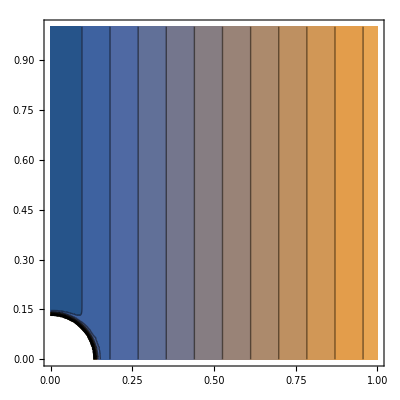

0.875

```mathematica
ρ0 = 1.0;
ρ1 = -1.0+1000;
δ = 0.01;
ContourPlot[ρ[x,y,0],{x,0,1},{y,0,1},Contours->20]
ρ[0.5,0.5,0]/ρ[1,1,0]
```

```mathematica
D[p[x,y,t],x]//FullSimplify
```

Cos[x] Sin[t] Sin[y]

```mathematica
D[p[x,y,t],y]//FullSimplify
```

Cos[y] Sin[t] Sin[x]

```mathematica
CellPrint[[HoldForm[fx[x,y,t]],"Output",AutoMultiplicationSymbol->True]]
```

CellPrint⟦fx[x,y,t],Output,AutoMultiplicationSymbol→True⟧

```mathematica
fy[x,y,t]//InputForm
```

Cos[y]*Sin[t]*Sin[x] + (4*Pi*μ1*Cos[t]*Sin[2*Pi*x]*Sin[2*Pi*y])/3 + y*Cos[t]^2*(y*Cos[Sin[t]] - x*Sin[Sin[t]]) - 
 y*Sin[t]*(3. + x*Cos[Sin[t]] + y*Sin[Sin[t]] + 499.5*(1 + Tanh[100.*(0.1 - 1.*Sqrt[x^2 + y^2])]))

```mathematica
ρ0 = 1.0;
ρ1 = 1.0+10;
μ0 = 0.001;
μ1 = -μ0+1;
δ = 0.01;
Manipulate[ContourPlot[fy[x,y,t],{x,0,1},{y,0,1},Contours->10,PlotLegends->Automatic],{t,0,0.1}]
```

```mathematica
(*Tangential traction at top and bottom face*)
μ[x,y,t](D[u[x,y,t],y]+ D[v[x,y,t],x])
```

0

```mathematica
(*Normal traction at top and bottom face*)
-p[x,y,t]+2μ[x,y,t]D[v[x,y,t],y]//InputForm
```

2*Cos[t]*(1. + 0.999*Cos[2*Pi*y]*Sin[2*Pi*x]) - Sin[t]*Sin[x]*Sin[y]

```mathematica
trac[x_,y_,t_]=-p[x,y,t]+2μ[x,y,t]D[v[x,y,t],y]
```

2 Cos[t] (1.+0.999 Cos[2 π y] Sin[2 π x])-Sin[t] Sin[x] Sin[y]

```mathematica
trac[0,1,t]-trac[1,1,t]
```

0.+Sin[1]^2 Sin[t]